```mathematica
x=0.9375;
b=3/4x;
```

## Intro

```mathematica
introVocals=Sound[{
SoundNote["G3",1/4x,"SynthVoice"],SoundNote["G3",1/4x,"SynthVoice"],SoundNote["G3",1/4x,"SynthVoice"],SoundNote["D4",1/3x,"SynthVoice"],SoundNote["E4",1/3x,"SynthVoice"],SoundNote["E4",1/3x,"SynthVoice"],SoundNote["E4",3/2x,"SynthVoice"],SoundNote[None,3/4x],SoundNote["G3",1/4x,"SynthVoice"],SoundNote["G3",1/4x,"SynthVoice"],SoundNote["G3",1/4x,"SynthVoice"],SoundNote["E4",1/3x,"SynthVoice"],SoundNote["F4",1/3x,"SynthVoice"],SoundNote["F4",1/3x,"SynthVoice"],SoundNote["F4",3/2x,"SynthVoice"],SoundNote[None,x],SoundNote["A3",1/4x,"SynthVoice"],SoundNote["A3",1/4x,"SynthVoice"],SoundNote["F4",1/3x,"SynthVoice"],SoundNote["E4",1/3x,"SynthVoice"],SoundNote["D4",1/3x,"SynthVoice"],SoundNote["F4",3/4x,"SynthVoice"],SoundNote["D4",1/4x,"SynthVoice"],SoundNote["E4",1/3x,"SynthVoice"],SoundNote["D4",1/3x,"SynthVoice"],SoundNote["C4",1/3x,"SynthVoice"],SoundNote["E4",1/4x,"SynthVoice"],SoundNote["D4",1/4x,"SynthVoice"],SoundNote["C4",1/4x,"SynthVoice"],SoundNote["D4",1/4x,"SynthVoice"],SoundNote["B3",3/2x,"SynthVoice"]
}];
```

```mathematica
introPianoRH=Sound[{
SoundNote[{"C5","E5"},3x,"NewAge"],SoundNote["B4",x,"NewAge"],SoundNote["D5",1/2x,"NewAge"],SoundNote["E5",7/2x,"NewAge"],SoundNote["F5",1/3x,"NewAge"],SoundNote["E5",1/3x,"NewAge"],SoundNote["D5",1/3x,"NewAge"],SoundNote["F5",x,"NewAge"],SoundNote["E5",1/3x,"NewAge"],SoundNote["D5",1/3x,"NewAge"],SoundNote["C5",1/3x,"NewAge"],SoundNote["E5",1/2x,"NewAge"],SoundNote["D5",1/2x,"NewAge"],SoundNote["B4",3x,"NewAge"],SoundNote["E5",1/4x,"NewAge"],SoundNote["D5",1/4x,"NewAge"],SoundNote["C5",1/4x,"NewAge"],SoundNote["E5",1/4x,"NewAge"]
}];

introPianoLH=Sound[{
SoundNote[{"A2","C3","E3"},x,"Piano"],SoundNote[{"A2","C3","E3"},x,"Piano"],SoundNote[{"A2","C3","E3"},x,"Piano"],SoundNote[{"G2","B2","D3"},x,"Piano"],SoundNote[{"A2","D3","F3"},x,"Piano"],SoundNote[{"A2","D3","F3"},x,"Piano"],SoundNote[{"A2","D3","F3"},x,"Piano"],SoundNote[{"A2","D3","F3"},x,"Piano"],SoundNote[{"A2","C3","F3"},x,"Piano"],SoundNote[{"A2","C3","F3"},x,"Piano"],SoundNote[{"G2","C3","E3"},x,"Piano"],SoundNote[{"G2","C3","E3"},x,"Piano"],SoundNote[{"G2","B2","D3"},x,"Piano"],SoundNote[{"G2","B2","D3"},x,"Piano"],SoundNote[{"G2","B2","D3"},x,"Piano"],SoundNote[{"G2","B2","D3"},x,"Piano"]
}];
```

```mathematica
marryVocals=Sound[{
SoundNote["G3",1/4x,"SynthVoice"],SoundNote["E4",1/4x,"SynthVoice"],SoundNote["E4",1/4x,"SynthVoice"],SoundNote["E4",1/4x,"SynthVoice"],SoundNote["D4",1/4x,"SynthVoice"],SoundNote["C4",1/4x,"SynthVoice"],SoundNote["C4",1/4x,"SynthVoice"],SoundNote["G3",1/4x,"SynthVoice"],SoundNote["A3",3/4x,"SynthVoice"]
}];

marryPiano=Sound[{
SoundNote["B4",x,"NewAge"],SoundNote[None,2x],SoundNote["E5",1/4x,"NewAge"],SoundNote["D5",1/4x,"NewAge"],SoundNote["C5",1/4x,"NewAge"],SoundNote["E5",1/4x,"NewAge"]
}];
```

## SongWriting

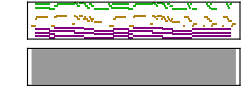

```mathematica
x=0.9375;
b=0.75;
Sound[{
Sound[introVocals,{-.75x+b,13.5x+b}],
Sound[introPianoRH,{0x+b,16x+b},SoundVolume->0.4],
Sound[introPianoLH,{0x+b,16x+b},SoundVolume->0.5],

Sound[introVocals,{15.25x+b,29.5x+b}],
Sound[introPianoRH,{16x+b,32x+b},SoundVolume->0.4],
Sound[introPianoLH,{16x+b,32x+b},SoundVolume->0.5],

Sound[marryVocals,{30.25x+b,33x+b}],Sound[marryPiano,{32x+b,36x+b},SoundVolume->0.4],
SoundNote[{"A2","C3","E3"},{32x+b,34x+b},"Piano",SoundVolume->0.5],SoundNote[{"A2","C3","E3"},{34x+b,36x+b},"Piano",SoundVolume->0.5],
Sound[marryVocals,{34.25x+b,37x+b}],Sound[marryPiano,{36x+b,40x+b},SoundVolume->0.4],
SoundNote[{"A2","C3","E3"},{36x+b,38x+b},"Piano",SoundVolume->0.5],SoundNote[{"A2","C3","E3"},{38x+b,40x+b},"Piano",SoundVolume->0.5],
Sound[marryVocals,{38.25x+b,41x+b}]
}]
```